# Project 1

## Environmental Setup

```mathematica
SetDirectory["/Users/kevinfisher/Documents/Math Modeling"];
Directory[]
```

SetDirectory::cdir: Cannot set current directory to /Users/kevinfisher/Documents/Math Modeling.

C:\Users\Rowan

```mathematica
printTable[data_,first_:3,last_:1]:=TableForm[Join[Take[data,first],{{"...","..."}},Take[data,-last]]]
```

```mathematica
q=80;
```

## Importing and Parsing Data

```mathematica
popData :=First[Import["C:\\Users\\Rowan\\Downloads\\Tanzania Population Data(1).xlsx"]];
```

### Urban Population

```mathematica
urbanPop=Transpose[{popData[[2;;,3]],popData[[2;;,4]]}];
urbanPop = Table[{urbanPop[[i,1]]-1960,urbanPop[[i,2]]},{i,1,Length[urbanPop]}];
printTable[urbanPop]
urbanPopGraph = ListPlot[urbanPop, Joined->True, PlotStyle->Blue, PlotLabel->"Urban Population",PlotLabels->"Urban",AxesLabel-> {"Year (since 1960)","Population"}]
```

0. | 527336.
1. | 558101.
2. | 590864.
... | ...
60. | 2.10426×10^7

-Graphics-

### Rural Population

```mathematica
ruralPop=Transpose[{popData[[2;;,3]],popData[[2;;,5]]}];
ruralPop = Table[{ruralPop[[i,1]]-1960,ruralPop[[i,2]]},{i,1,Length[ruralPop]}];
printTable[ruralPop]
ruralPopGraph = ListPlot[ruralPop, Joined->True, PlotStyle->Red, PlotLabel->"Rural Population",PlotLabels->"Rural",AxesLabel-> {"Year (since 1960)","Population"}]
```

0. | 9.52482×10^6
1. | 9.78859×10^6
2. | 1.00611×10^7
... | ...
60. | 3.86916×10^7

-Graphics-

### Total Population

0. | 1.00522×10^7
1. | 1.03467×10^7
2. | 1.0652×10^7
... | ...
60. | 5.97342×10^7

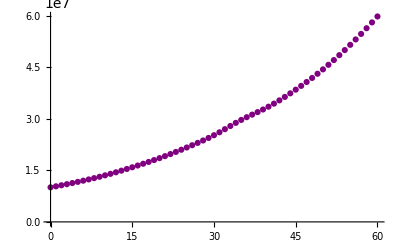

```mathematica
totalPop = Table[{urbanPop[[i,1]],urbanPop[[i,2]]+ruralPop[[i,2]]},{i,1,Length[urbanPop]}];
printTable[totalPop]
totalPopGraph = ListPlot[totalPop, PlotStyle->Purple]
```

### Visualizing the Data Sets

```mathematica
Show[urbanPopGraph, ruralPopGraph, totalPopGraph, PlotRange->All, PlotLabel->"Populations"]
```

-Graphics-

## Finding the Change

### Urban Population

```mathematica
durbanPop = Table[{urbanPop[[i+1,1]],urbanPop[[i+1,2]]-urbanPop[[i,2]]},{i,1,Length[urbanPop]-1}];
printTable[durbanPop]
durbanPopGraph=ListPlot[durbanPop,Joined->True,PlotLabel->"Change in Urban Population", PlotLabels->"Urban",AxesLabel->{"Year (since 1960)","Change in Population"},PlotStyle->Blue]
```

1. | 30765.
2. | 32763.
3. | 34762.
... | ...
60. | 1.03069×10^6

-Graphics-

### Rural Population

```mathematica
druralPop = Table[{ruralPop[[i+1,1]],ruralPop[[i+1,2]]-ruralPop[[i,2]]},{i,1,Length[ruralPop]-1}];
printTable[druralPop]
durbanPopGraph=ListPlot[druralPop,Joined->True,PlotLabel->"Change in Rural Population", PlotLabels->"Rural",AxesLabel->{"Year (since 1960)","Change in Population"},PlotStyle->Red]
```

1. | 263779.
2. | 272496.
3. | 281480.
... | ...
60. | 698065.

-Graphics-

### Total Population

```mathematica
dtotalPop = Table[{totalPop[[i+1,1]],totalPop[[i+1,2]]-totalPop[[i,2]]},{i,1,Length[totalPop]-1}];
printTable[dtotalPop]
durbanPopGraph=ListPlot[dtotalPop,Joined->True,PlotLabel->"Change in Total Population", PlotLabels->"Total",AxesLabel->{"Year (since 1960)","Change in Population"},PlotStyle->Purple]
```

1. | 294544.
2. | 305259.
3. | 316242.
... | ...
60. | 1.72875×10^6

-Graphics-

## Finding a Growth Model

### Parameters

```mathematica
limit = 2976857550
migration[n_] := 0.0014
```

2976857550

### Total Population

```mathematica
totalLG = Table[{totalPop[[i,2]]*(limit-totalPop[[i,2]]),dtotalPop[[i,2]]},{i,1,Length[dtotalPop]}];
totalLGGraph =ListPlot[totalLG, PlotStyle->Purple];
totalFit =Fit[totalLG,{x},x]
totalFitGraph = Plot[totalFit,{x,0,1.6*^17},PlotStyle->Green];
Show[totalFitGraph,totalLGGraph]
```

1.00968×10^-11 x

-Graphics-

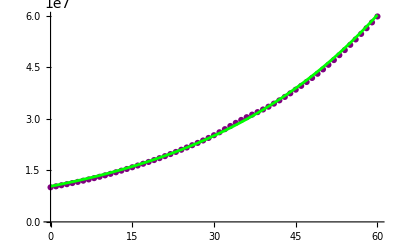

```mathematica
totalModel[0]=1.0052151*^7;
Do[totalModel[n]=1.009682670393068*^-11(limit-totalModel[n-1])totalModel[n-1]+totalModel[n-1], {n,1,q}];
totalModelGraph =ListPlot[Table[{totalPop[[i,1]],totalModel[i]},{i,1,Length[totalPop]}],PlotStyle->  Green, Joined->True];
Show[totalPopGraph,totalModelGraph]
```

### Urban Population

#### Logistic Growth

```mathematica
urbanLG = Table[{urbanPop[[i,2]]*(limit-totalModel[i]),durbanPop[[i,2]]},{i,1,Length[durbanPop]}];
urbanLGGraph =ListPlot[urbanLG, PlotStyle->Blue];
urbanFit =Fit[urbanLG,{x},x]
urbanFitGraph = Plot[urbanFit,{x,0,6*^16},PlotStyle->Green];
Show[urbanFitGraph,urbanLGGraph]
```

1.81125×10^-11 x

-Graphics-

```mathematica
urbanModel[0]=527336;
Do[urbanModel[n]=1.810992514081808*^-11(limit-totalModel[n-1])urbanModel[n-1]+urbanModel[n-1]+((migration[n])(totalModel[n-1]-urbanModel[n-1])), {n,1,q}];
urbanModelGraph =ListPlot[Table[{urbanPop[[i,1]],urbanModel[i]},{i,1,Length[urbanPop]}],PlotStyle->  Green];
Show[urbanPopGraph,urbanModelGraph]
```

-Graphics-

#### Exponential Growth

0.0530783 x

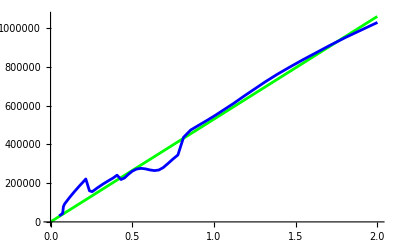

```mathematica
urbanEXP = Table[{urbanPop[[i,2]],durbanPop[[i,2]]},{i,1,Length[durbanPop]}];
urbanEXPGraph =ListPlot[urbanEXP, Joined -> True, PlotStyle->Blue];
urbanEXPFit=Fit[urbanEXP,{x},x]
urbanEXPFitGraph = Plot[urbanEXPFit,{x,0,2*^7},PlotStyle->Green];
Show[urbanEXPFitGraph,urbanEXPGraph,PlotRange -> All]
```

```mathematica
urbanEXPModel[0]=527336;
Do[urbanEXPModel[n]=1.0530783*urbanEXPModel[n-1], {n,1,Length[urbanEXP]}];
urbanEXPModelGraph =ListPlot[Table[{urbanPop[[i,1]],urbanEXPModel[i]},{i,1,Length[urbanPop]}],PlotStyle->  Green, Joined->True];
Show[urbanPopGraph,urbanEXPModelGraph]
```

-Graphics-

### Rural Population

#### Logistic Growth

```mathematica
ruralLG = Table[{(ruralPop[[i,2]]*(limit-totalPop[[i,2]])),druralPop[[i,2]]},{i,1,Length[druralPop]}];
ruralLGGraph =ListPlot[ruralLG, Joined -> True, PlotStyle->Red];
ruralFit =Fit[ruralLG,{1,x},x]
ruralFitGraph = Plot[ruralFit,{x,0,1.1*^17},PlotStyle->Green];
Show[ruralFitGraph,ruralLGGraph]
```

144402.+5.39089×10^-12 x

-Graphics-

```mathematica
ruralModel[0]=9.524815*^6;
Do[ruralModel[n]=7.370106116931787*^-12 (limit-totalModel[n-1])ruralModel[n-1]+ruralModel[n-1]-((migration[n])(totalModel[n-1]-urbanModel[n-1])), {n,1,Length[totalLG]}];
ruralModelGraph =ListPlot[Table[{ruralPop[[i,1]],ruralModel[i]},{i,1,Length[ruralPop]}],PlotStyle->  Green, Joined->True];
Show[ruralPopGraph,ruralModelGraph]
```

-Graphics-

#### Square Root Growth

2932.57+53.018 x

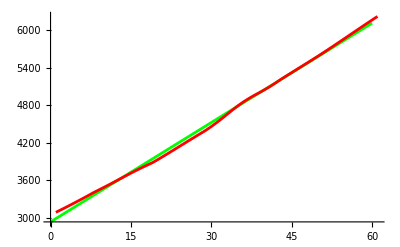

```mathematica
ruralSQ = Table[{i,Sqrt[ruralPop[[i,2]]]},{i,1,Length[ruralPop]}];
ruralSQGraph =ListPlot[ruralSQ, Joined -> True, PlotStyle->Red];
ruralSQFit =Fit[ruralSQ,{1,x},x]
ruralSQFitGraph = Plot[ruralSQFit,{x,0,60},PlotStyle->Green];
Show[ruralSQFitGraph,ruralSQGraph, PlotRange->All]
```

```mathematica
f[n_]:=(53.018n+2985.59)^2
ruralSQFitTable = Table[{i,f[i]},{i,1,q}];
ruralSQModelGraph =ListPlot[ruralSQFitTable,PlotStyle->  Green, Joined->True];
Show[ruralPopGraph,ruralSQModelGraph]
```

-Graphics-

## When Urban Beats Rural

### Change Plot Colors

```mathematica
ruralSQModelGraph =ListPlot[ruralSQFitTable,PlotStyle->  LightRed, Joined->True];
urbanModelGraph =ListPlot[Table[{i,urbanModel[i]},{i,1,q}],PlotStyle->  LightBlue, Joined->True];
```

### Graph

```mathematica
Show[ruralSQModelGraph, urbanModelGraph,urbanPopGraph, ruralPopGraph, Graphics[{AbsolutePointSize[10],Point[{77,5*10^7}]}], PlotLabel->"Model",PlotRange->All]
```

-Graphics-

The Urban Population will surpass the Rural Population at year 77 or 2037